# Wind Turbine Designer Tool

## Math Model

### Constants

#### Air Density (δa)

```mathematica
δa=1.225;
```

```mathematica
CPmax = 0.5925925925925926;
```

### Equations

#### Wind Power

```mathematica
Pw[Vw_, R_, CP_]:= 1/2 CP δa Vw^3 R^2 π;
```

#### Rotor radius

```mathematica
RotorRadius[Po_,  Vw_, Cp_]:=√((2*Po)/(δa * Vw^3*Cp * π));
```

#### Tip Speed Ratio (λ)

```mathematica
TSR[Vw_, rpm_, R_]:= R*rpm*π / (Vw * 30);
```

#### Revolutions Per Minutes

```mathematica
RPM[Vw_, λ_,  R_]:= (λ * 30 * Vw)/(R*π);
```

```mathematica
RPM2[Vw_, rpmmax_,λ_,R_]:= Piecewise[{{RPM[Vw,λ, R], RPM[Vw,λ, R] ≤rpmmax  }, {rpmmax,  RPM[Vw,λ, R]>rpmmax}}]
```

#### Average Chord Length

```mathematica
AverageChordLength[R_,Sp_,Cl_,Z_]:=(R * Sp)/(Cl * Z);
```

#### Chord Length List

```mathematica
ChordLength[R_, Vw_, Z_, Cl_, λ_, Vr_]:=(2 π R 8 Vw)/(Z 9 Cl λ Vr);
```

#### Solidity

```mathematica
Solidity[R_,l_,Z_]:=(Z*l)/(π*R);
```

#### Blade Velocity

```mathematica
Vu[ R_, rpm_]:=R*rpm*π/30;
```

#### Relative Wind Velocity

```mathematica
Vr[Vw_, Vu_]:=√((2/3 Vw)^2+ Vu^2);
```

#### Wind Angle (θ)

```mathematica
theta[λr_]:=ArcTan[2/(3 λr)]/ Degree;
```

#### Forces on the Blade

```mathematica
Fblade[CFT_, Vr_, L_, dr_]:=1/2 CFT δa Vr^2 L dr;
```

## Airfoil Data

### Airfoil Specifications: A18

#### Aerodynamic Data

```mathematica
A18AlphaData=List[-9.5,-9.25,-9.0,-8.75,-8.5,-8.25,-8.0,-7.75,-7.5,-7.25,-7.0,-6.75,-6.5,-6.25,-6.0,-5.75,-5.5,-5.25,-5.0,-4.75,-4.5,-4.25,-4.0,-3.75,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-2.0,-1.75,-1.5,-1.25,-1.0,-0.75,-0.5,-0.25,0.0,0.25,0.5,0.75,1.0,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.0,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25,12.5];
A18CLData=List[-0.4443,-0.4551,-0.4655,-0.4733,-0.4792,-0.4593,-0.431,-0.4061,-0.3775,-0.3422,-0.307,-0.2723,-0.2369,-0.2006,-0.1662,-0.1313,-0.0951,-0.0624,-0.0272,0.0096,0.0415,0.0754,0.1105,0.1409,0.1742,0.2073,0.2383,0.2721,0.3022,0.334,0.365,0.395,0.4255,0.4552,0.4838,0.5113,0.5352,0.5594,0.5876,0.615,0.6424,0.6695,0.6965,0.7235,0.7503,0.7769,0.8032,0.8295,0.8553,0.881,0.9061,0.9306,0.9524,0.9755,0.9928,1.0127,1.0353,1.0573,1.0767,1.0964,1.1174,1.1387,1.1585,1.1746,1.1923,1.2095,1.2269,1.2443,1.2608,1.2761,1.2905,1.3036,1.3151,1.3252,1.3333,1.3375,1.3364,1.3326,1.3263,1.3179,1.3064,1.2937,1.2783,1.2608,1.2421,1.2217,1.2003,1.1776,1.154];
A18CDData=List[0.086,0.08249,0.07857,0.07371,0.06745,0.02683,0.02267,0.02145,0.02003,0.01853,0.01806,0.01798,0.01752,0.01752,0.01749,0.01659,0.01593,0.01542,0.01483,0.01429,0.01368,0.01323,0.01285,0.01257,0.01222,0.01194,0.01166,0.01138,0.01115,0.01091,0.01074,0.01055,0.01032,0.01014,0.00984,0.00951,0.00905,0.00868,0.00876,0.00887,0.009,0.00914,0.00931,0.00949,0.00967,0.00988,0.0101,0.01034,0.01062,0.01092,0.01127,0.01165,0.01225,0.01282,0.01405,0.01509,0.01578,0.01652,0.01761,0.01869,0.0196,0.02042,0.02142,0.02285,0.02402,0.02525,0.02649,0.02768,0.02898,0.03054,0.03232,0.03452,0.03746,0.04029,0.04266,0.04499,0.04725,0.04975,0.05252,0.05553,0.0591,0.06296,0.06751,0.07275,0.07869,0.08555,0.09339,0.10243,0.11286];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
A18FCL = Interpolation[Thread[{A18AlphaData, A18CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
A18FCD= Interpolation[Thread[{A18AlphaData, A18CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[A18FCL[α],"CL"], Labeled[A18FCD[α],"CD"]},{α, -9.5, 12.5}, AxesLabel->{"Angel α","Coefficient"}]]
```

-Graphics-

#### Airfoil Geometry

```mathematica
A18Geometry = List[{1.00000000,0.00614000},{0.94999999,0.01817000},{0.89999998,0.02858000},{0.80000001,0.04624000},{0.69999999,0.06056000},{0.60000002,0.07197000},{0.55000001,0.07612000},{0.50000000,0.07975000},{0.44999999,0.08293000},{0.40000001,0.08376000},{0.34999999,0.08466000},{0.30000001,0.08383000},{0.25000000,0.08065000},{0.20000000,0.07601000},{0.15000001,0.07026000},{0.10000000,0.06234000},{0.07500000,0.05660000},{0.05000000,0.04923000},{0.02500000,0.03947000},{0.01250000,0.03239000},{0.00000000,0.01865000},{0.01250000,0.00781000},{0.02500000,0.00357000},{0.05000000,0.00075000},{0.07500000,0.00000000},{0.10000000,0.00006000},{0.15000001,0.00200000},{0.20000000,0.00475000},{0.25000000,0.00806000},{0.30000001,0.01038000},{0.34999999,0.01353000},{0.40000001,0.01657000},{0.44999999,0.01780000},{0.50000000,0.01884000},{0.55000001,0.01980000},{0.60000002,0.01998000},{0.69999999,0.01924000},{0.80000001,0.01452000},{0.89999998,0.00813000},{0.94999999,0.00434000},{1.00000000,0.00000000}];
```

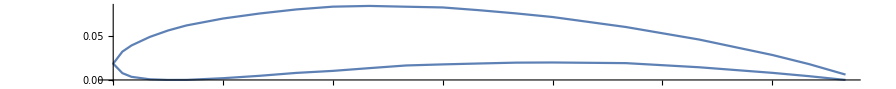

```mathematica
ListLinePlot[A18Geometry, AspectRatio->.1]
```

### Airfoil Specifications: BW3

#### Aerodynamic Data

```mathematica
BW3AlphaData=List[-8.0,-7.75,-7.5,-7.25,-7.0,-6.75,-6.5,-6.0,-5.75,-5.5,-5.0,-4.75,-4.5,-4.25,-4.0,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-2.0,-1.75,-1.5,-1.25,-1.0,-0.75,-0.5,-0.25,0.0,0.25,0.5,0.75,1.0,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25,12.5,12.75,13.0,13.25,13.5,13.75,14.0,14.25,14.5,14.75,15.0,15.25,15.5,15.75,16.0,16.25,16.5,16.75,17.0,17.25,17.5,17.75,18.0,18.25];
BW3CLData=List[-0.3875,-0.3885,-0.3893,-0.3712,-0.347,-0.3222,-0.296,-0.2713,-0.2344,-0.1924,-0.0619,-0.0214,0.0225,0.0693,0.1149,0.1908,0.223,0.2523,0.2811,0.3092,0.3371,0.3647,0.3921,0.4193,0.446,0.4722,0.4982,0.5245,0.5509,0.5773,0.6039,0.6305,0.6571,0.6829,0.7083,0.7332,0.7579,0.782,0.8053,0.8279,0.8495,0.8707,0.8917,0.9122,0.9247,0.9495,0.9744,0.9994,1.0237,1.0479,1.0726,1.0973,1.1212,1.1438,1.1677,1.1914,1.2151,1.3756,1.397,1.4185,1.4388,1.4587,1.477,1.4936,1.5116,1.5301,1.5475,1.5646,1.5814,1.5976,1.6116,1.6222,1.6296,1.6349,1.6426,1.6506,1.658,1.6647,1.6701,1.6753,1.6808,1.6845,1.688,1.6901,1.692,1.6923,1.6908,1.6877,1.683,1.6742,1.6635,1.6541,1.6419,1.6284,1.6116,1.5942,1.5734,1.5534,1.5278,1.5,1.4675,1.3859];
BW3CDData=List[0.10068,0.09827,0.09556,0.09051,0.08599,0.07931,0.07743,0.07139,0.06632,0.06082,0.01612,0.01363,0.01263,0.01181,0.01121,0.01038,0.01012,0.00984,0.00962,0.00947,0.00941,0.00943,0.00947,0.00945,0.0096,0.00967,0.00968,0.00968,0.00975,0.0098,0.00979,0.00975,0.0097,0.00971,0.00974,0.0097,0.00978,0.00992,0.01015,0.01045,0.0109,0.01142,0.01199,0.01262,0.01403,0.0143,0.01455,0.01478,0.01507,0.01537,0.01563,0.01592,0.01627,0.01672,0.01703,0.01738,0.01775,0.0192,0.01972,0.02019,0.02078,0.02138,0.02212,0.02301,0.02376,0.02444,0.02521,0.02597,0.02672,0.02747,0.02831,0.02919,0.03025,0.03159,0.03278,0.03399,0.03526,0.03663,0.03816,0.03974,0.0413,0.04314,0.04506,0.04722,0.04945,0.05195,0.05477,0.05787,0.06128,0.06536,0.06992,0.07448,0.07963,0.08527,0.09174,0.09865,0.10659,0.1148,0.12467,0.13543,0.14822,0.17722];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
BW3FCL = Interpolation[Thread[{BW3AlphaData, BW3CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
BW3FCD= Interpolation[Thread[{BW3AlphaData, BW3CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[BW3FCL[α],"CL"], Labeled[BW3FCD[α],"CD"]},{α, -8, 16}, AxesLabel->{"Angel α","Coefficient"}]]
```

-Graphics-

#### Airfoil Geometry

```mathematica
BW3Geometry = List[{1.00000000,0.00349500},{0.99754000,0.00537700},{0.99070001,0.00983200},{0.98036999,0.01482900},{0.96697998,0.01922400},{0.95043999,0.02280900},{0.93063998,0.02586900},{0.90775001,0.02891900},{0.88202000,0.03237000},{0.85369998,0.03637000},{0.82309002,0.04084100},{0.79048002,0.04562100},{0.75616002,0.05051900},{0.72043002,0.05535800},{0.68358999,0.05998300},{0.64594001,0.06426400},{0.60777998,0.06808700},{0.56936997,0.07136400},{0.53099000,0.07401900},{0.49265000,0.07600400},{0.45434999,0.07727300},{0.41637999,0.07782800},{0.37887001,0.07770600},{0.34204000,0.07695100},{0.30609000,0.07559600},{0.27120000,0.07364000},{0.23760000,0.07104800},{0.20548999,0.06776400},{0.17504001,0.06373800},{0.14647999,0.05898200},{0.11999000,0.05360400},{0.09576000,0.04781100},{0.07395000,0.04188100},{0.05468000,0.03611300},{0.03811000,0.03075000},{0.02433000,0.02568200},{0.01338000,0.02038100},{0.00548000,0.01437600},{0.00098000,0.00757500},{0.00000000,0.00237400},{0.00098000,-0.00267500},{0.00548000,-0.00851100},{0.01338000,-0.01219600},{0.02433000,-0.01394700},{0.03811000,-0.01421700},{0.05468000,-0.01261100},{0.07395000,-0.00830300},{0.09576000,-0.00175700},{0.11999000,0.00531900},{0.14647999,0.01174500},{0.17504001,0.01742100},{0.20548999,0.02241300},{0.23760000,0.02661000},{0.27120000,0.03005500},{0.30609000,0.03288100},{0.34204000,0.03514900},{0.37887001,0.03687700},{0.41637999,0.03804000},{0.45434999,0.03851600},{0.49265000,0.03818200},{0.53099000,0.03704800},{0.56936997,0.03525200},{0.60777998,0.03298300},{0.64594001,0.03038300},{0.68358999,0.02749400},{0.72043002,0.02432000},{0.75616002,0.02090100},{0.79048002,0.01733800},{0.82309002,0.01375900},{0.85369998,0.01029500},{0.88202000,0.00704100},{0.90775001,0.00403300},{0.93063998,0.00126600},{0.95043999,-0.00141100},{0.96697998,-0.00458000},{0.98036999,-0.00742500},{0.99070001,-0.00752400},{0.99754000,-0.00489700},{1.00000000,-0.00312200}];
```

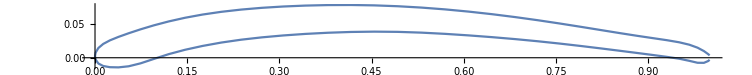

```mathematica
ListLinePlot[BW3Geometry, AspectRatio->.1]
```

### Airfoil Specifications: NACA63A210

#### Aerodynamic Data

```mathematica
NACA63A210AlphaData=List[-11.0,-10.75,-10.5,-10.25,-10.0,-9.75,-9.5,-9.25,-9.0,-8.75,-8.5,-8.25,-8.0,-7.75,-7.5,-7.25,-7.0,-6.75,-6.5,-6.25,-6.0,-5.75,-5.5,-5.25,-5.0,-4.75,-4.5,-4.25,-4.0,-3.75,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-2.0,-1.5,-1.25,-1.0,-0.75,-0.5,-0.25,0.0,0.25,0.5,0.75,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.0,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25,12.5,12.75,13.0,13.25,13.5,13.75,14.0,14.25];
NACA63A210CLData=List[-0.6337,-0.8334,-0.8484,-0.8449,-0.8384,-0.8292,-0.8174,-0.8034,-0.7871,-0.7685,-0.7482,-0.7263,-0.7026,-0.6818,-0.6578,-0.6334,-0.609,-0.5844,-0.5597,-0.5347,-0.5092,-0.4843,-0.4595,-0.4337,-0.4075,-0.3812,-0.3547,-0.3279,-0.3013,-0.2741,-0.2472,-0.2201,-0.1933,-0.1669,-0.1421,-0.118,-0.0916,-0.0384,-0.0116,0.0158,0.0434,0.0713,0.0992,0.1273,0.1554,0.1832,0.2112,0.2671,0.295,0.3228,0.3501,0.3771,0.4036,0.4296,0.4559,0.4871,0.5222,0.5549,0.5846,0.6082,0.6326,0.6574,0.6824,0.7074,0.7321,0.7571,0.7817,0.8059,0.829,0.8509,0.8739,0.8967,0.9194,0.9412,0.9626,0.9835,1.0041,1.0248,1.0457,1.0658,1.0814,1.0966,1.1147,1.1313,1.1461,1.1589,1.1694,1.1773,1.1811,1.183,1.1842,1.1841,1.1836,1.1829,1.1788,1.1733,1.1627,1.1481,1.1267,1.0914];
NACA63A210CDData=List[0.10321,0.04821,0.04417,0.0415,0.03883,0.03618,0.03364,0.03122,0.02902,0.02713,0.02553,0.02426,0.02351,0.02187,0.0212,0.02052,0.01982,0.01913,0.01848,0.01788,0.01741,0.01681,0.01617,0.01576,0.0154,0.01507,0.01477,0.01449,0.01409,0.01381,0.01352,0.01328,0.01298,0.01257,0.01184,0.01107,0.01077,0.01034,0.01017,0.01006,0.00999,0.00993,0.00986,0.00979,0.00974,0.00969,0.00965,0.00955,0.00951,0.00953,0.00955,0.0096,0.00978,0.00975,0.00968,0.00958,0.00962,0.01009,0.01061,0.01102,0.01137,0.01169,0.012,0.01233,0.01269,0.01303,0.01341,0.01384,0.01441,0.01512,0.01569,0.01625,0.01683,0.01751,0.01825,0.01904,0.01986,0.02066,0.02138,0.02219,0.02363,0.02519,0.02624,0.02747,0.02886,0.03043,0.03214,0.03398,0.0358,0.03763,0.03946,0.04148,0.0437,0.04611,0.04924,0.05299,0.05813,0.06423,0.07139,0.08211];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
NACA63A210FCL = Interpolation[Thread[{NACA63A210AlphaData, NACA63A210CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
NACA63A210FCD= Interpolation[Thread[{NACA63A210AlphaData, NACA63A210CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[NACA63A210FCL[α],"CL"], Labeled[NACA63A210FCD[α],"CD"]},{α, -11, 14}, AxesLabel->{"Angel α","Coefficient"}]]
```

-Graphics-

#### Airfoil Geometry

```mathematica
NACA63A210Geometry = List[{1.00000000,0.00021000},{0.95025998,0.00769000},{0.90050000,0.01519000},{0.85071999,0.02254000},{0.80074000,0.02974000},{0.75060999,0.03624000},{0.70051998,0.04227000},{0.65041000,0.04772000},{0.60027999,0.05245000},{0.55012000,0.05637000},{0.49994001,0.05943000},{0.44975001,0.06151000},{0.39954999,0.06247000},{0.34935001,0.06219000},{0.29916000,0.06060000},{0.24898000,0.05764000},{0.19881999,0.05328000},{0.14869000,0.04729000},{0.09863000,0.03917000},{0.07364000,0.03400000},{0.04869000,0.02769000},{0.02384000,0.01944000},{0.01151000,0.01367000},{0.00664000,0.01058000},{0.00423000,0.00868000},{0.00000000,0.00000000},{0.00577000,-0.00756000},{0.00836000,-0.00900000},{0.01349000,-0.01125000},{0.02616000,-0.01522000},{0.05131000,-0.02047000},{0.07636000,-0.02428000},{0.10137000,-0.02725000},{0.15131000,-0.03167000},{0.20118000,-0.03468000},{0.25102001,-0.03662000},{0.30083999,-0.03764000},{0.35065001,-0.03771000},{0.40044999,-0.03689000},{0.45025000,-0.03523000},{0.50006002,-0.03283000},{0.54988003,-0.02985000},{0.59972000,-0.02641000},{0.64959002,-0.02262000},{0.69948000,-0.01861000},{0.74939001,-0.01464000},{0.79926002,-0.01104000},{0.84928000,-0.00812000},{0.89950001,-0.00539000},{0.94973999,-0.00279000},{1.00000000,-0.00021000}];
```

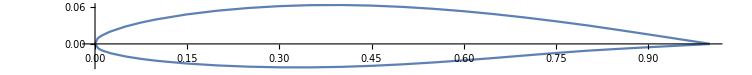

```mathematica
ListLinePlot[NACA63A210Geometry, AspectRatio->.1]
```

### Airfoil Specifications: NACA4415

#### Aerodynamic Data

```mathematica
NACA4415AlphaData=List[-15.75,-15.5,-15.25,-15.0,-14.75,-14.5,-14.25,-14.0,-13.75,-13.5,-13.25,-13.0,-12.75,-12.5,-12.25,-12.0,-11.75,-11.5,-11.25,-11.0,-10.75,-10.5,-10.25,-10.0,-9.75,-9.5,-9.25,-9.0,-8.75,-8.5,-8.25,-8.0,-7.75,-7.5,-7.0,-6.75,-6.5,-6.25,-6.0,-5.75,-5.25,-5.0,-4.75,-4.5,-4.25,-4.0,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-1.75,-1.5,-1.0,-0.75,-0.5,-0.25,0.0,0.5,0.75,1.0,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.0,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25,12.5,12.75,13.0,13.25,13.5,13.75,14.0,14.25,14.5,14.75,15.0,15.25,15.5,15.75,16.0,16.25,16.5,16.75,17.0,17.25,17.5,17.75,18.0,18.25,18.5,18.75,19.0,19.25];
NACA4415CLData=List[-0.7406,-0.7675,-0.8007,-0.8372,-0.8787,-0.9121,-0.9198,-0.917,-0.9113,-0.8995,-0.889,-0.8771,-0.8565,-0.8435,-0.8244,-0.8001,-0.7735,-0.7591,-0.7342,-0.7061,-0.6796,-0.6594,-0.6297,-0.5955,-0.5687,-0.5408,-0.5074,-0.4795,-0.4519,-0.4195,-0.3955,-0.366,-0.3409,-0.3136,-0.2623,-0.2375,-0.2119,-0.1874,-0.1619,-0.1377,-0.0886,-0.0641,-0.04,-0.016,0.0081,0.0317,0.079,0.1026,0.1258,0.1494,0.1724,0.1958,0.2419,0.2651,0.3111,0.3335,0.3564,0.3787,0.4015,0.4453,0.4657,0.4863,0.5045,0.5222,0.5388,0.5552,0.5731,0.6911,0.7566,0.7904,0.8212,0.857,0.8899,0.9066,0.9225,0.9378,0.953,0.9688,0.984,1.0006,1.0166,1.0334,1.05,1.0667,1.0841,1.1001,1.1174,1.1332,1.1487,1.1653,1.1801,1.1947,1.2087,1.2226,1.2355,1.2471,1.2584,1.2702,1.2814,1.2947,1.3054,1.3182,1.3291,1.3416,1.3519,1.363,1.3729,1.3823,1.3925,1.3999,1.4089,1.4155,1.422,1.4267,1.4313,1.4339,1.4377,1.439,1.4412,1.4409,1.4426,1.4415,1.4406,1.44,1.4379,1.4346,1.4337,1.4312,1.4274,1.4221,1.4173,1.4145,1.4107,1.4053,1.3988];
NACA4415CDData=List[0.08436,0.07768,0.07032,0.06289,0.05492,0.04605,0.03781,0.03334,0.03073,0.02885,0.02742,0.02626,0.02512,0.02399,0.02291,0.02196,0.02109,0.02045,0.0197,0.01899,0.01825,0.01769,0.01709,0.01648,0.01592,0.01543,0.01492,0.01446,0.01408,0.01361,0.01328,0.0129,0.01259,0.01228,0.01174,0.01151,0.0113,0.01111,0.01094,0.01079,0.01052,0.0104,0.01029,0.01018,0.0101,0.00999,0.00984,0.00979,0.00973,0.00968,0.00964,0.00959,0.00953,0.00951,0.00948,0.00947,0.00945,0.00944,0.00942,0.00935,0.00931,0.00919,0.00909,0.00895,0.00886,0.00876,0.00863,0.00889,0.0092,0.00938,0.0096,0.00977,0.00999,0.01013,0.0103,0.01044,0.01058,0.01073,0.0109,0.01107,0.01127,0.01147,0.0117,0.01195,0.01219,0.01249,0.01277,0.01311,0.01348,0.01383,0.01427,0.01473,0.01524,0.01576,0.01636,0.01704,0.01777,0.01849,0.01927,0.01996,0.02082,0.02159,0.02249,0.02333,0.02432,0.0253,0.02639,0.02754,0.02867,0.03004,0.03133,0.03285,0.03442,0.0362,0.03804,0.04012,0.04214,0.04445,0.04674,0.04934,0.05179,0.05459,0.05743,0.0603,0.06339,0.06666,0.0697,0.07298,0.07648,0.08021,0.08393,0.08742,0.09108,0.095,0.0991];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
NACA4415FCL = Interpolation[Thread[{NACA4415AlphaData, NACA4415CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
NACA4415FCD= Interpolation[Thread[{NACA4415AlphaData, NACA4415CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[NACA4415FCL[α],"CL"], Labeled[NACA4415FCD[α],"CD"]},{α, -15, 20}, AxesLabel->{"Angel α","Coefficient"}]]
```

-Graphics-

#### Airfoil Geometry

```mathematica
NACA4415Geometry = List[{1.00000000,0.00000000},{0.99892998,0.00039000},{0.99572003,0.00156000},{0.99039000,0.00349000},{0.98295999,0.00610000},{0.97346997,0.00932000},{0.96193999,0.01303000},{0.94844002,0.01716000},{0.93300998,0.02166000},{0.91573000,0.02652000},{0.89668000,0.03171000},{0.87592000,0.03717000},{0.85355002,0.04283000},{0.82967001,0.04863000},{0.80438000,0.05453000},{0.77779001,0.06048000},{0.75000000,0.06642000},{0.72114003,0.07227000},{0.69134003,0.07795000},{0.66071999,0.08341000},{0.62941003,0.08858000},{0.59754997,0.09341000},{0.56525999,0.09785000},{0.53270000,0.10185000},{0.50000000,0.10538000},{0.46730000,0.10837000},{0.43474001,0.11076000},{0.40245000,0.11248000},{0.37059000,0.11345000},{0.33928001,0.11361000},{0.30866000,0.11294000},{0.27886000,0.11141000},{0.25000000,0.10903000},{0.22221000,0.10584000},{0.19562000,0.10190000},{0.17033000,0.09726000},{0.14645000,0.09195000},{0.12408000,0.08607000},{0.10332000,0.07970000},{0.08427000,0.07283000},{0.06699000,0.06541000},{0.05156000,0.05753000},{0.03806000,0.04937000},{0.02653000,0.04118000},{0.01704000,0.03303000},{0.00961000,0.02489000},{0.00428000,0.01654000},{0.00107000,0.00825000},{0.00000000,0.00075000},{0.00107000,-0.00566000},{0.00428000,-0.01102000},{0.00961000,-0.01590000},{0.01704000,-0.02061000},{0.02653000,-0.02502000},{0.03806000,-0.02915000},{0.05156000,-0.03281000},{0.06699000,-0.03582000},{0.08427000,-0.03817000},{0.10332000,-0.03991000},{0.12408000,-0.04106000},{0.14645000,-0.04166000},{0.17033000,-0.04177000},{0.19562000,-0.04147000},{0.22221000,-0.04078000},{0.25000000,-0.03974000},{0.27886000,-0.03845000},{0.30866000,-0.03700000},{0.33928001,-0.03547000},{0.37059000,-0.03390000},{0.40245000,-0.03229000},{0.43474001,-0.03063000},{0.46730000,-0.02891000},{0.50000000,-0.02713000},{0.53270000,-0.02529000},{0.56525999,-0.02340000},{0.59754997,-0.02149000},{0.62941003,-0.01958000},{0.66071999,-0.01772000},{0.69134003,-0.01596000},{0.72114003,-0.01430000},{0.75000000,-0.01277000},{0.77779001,-0.01136000},{0.80438000,-0.01006000},{0.82967001,-0.00886000},{0.85355002,-0.00775000},{0.87592000,-0.00674000},{0.89668000,-0.00583000},{0.91573000,-0.00502000},{0.93300998,-0.00431000},{0.94844002,-0.00364000},{0.96193999,-0.00297000},{0.97346997,-0.00227000},{0.98295999,-0.00156000},{0.99039000,-0.00092000},{0.99572003,-0.00042000},{0.99892998,-0.00011000},{1.00000000,0.00000000}];
```

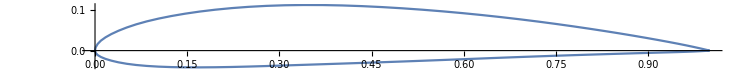

```mathematica
ListLinePlot[NACA4415Geometry, AspectRatio->.1]
```

## Designer

### Design Parameters

#### Air Velocity

```mathematica
Vw = 15;
```

#### Proposed RPM

```mathematica
rpm1 =750;
```

#### Number of Blades

```mathematica
Z1 = 3;
```

#### Number of Ribs (Blade Sections)

```mathematica
Nr = 20;
```

#### Design Power

```mathematica
Pd = 5000;
```

### Common Calculations

#### Calculate the rotor radius

```mathematica
R1 = Round[RotorRadius[Pd, Vw , .45], .01]
```

1.31

#### Calculate the “Tip Speed Ratio” (λ)

```mathematica
λd = TSR[Vw, rpm1, R1]
```

6.85914

```mathematica
TSRD[V_]:= Piecewise[{{λd,RPM[V,λd, R1] ≤ rpm1},{ TSR[V, rpm1, R1],RPM[V,λd, R1] > rpm1}}];
```

#### Differential of the radius (Δr)

```mathematica
Δr =(R1 - 0.10*R1) / (Nr -1)
```

0.0620526

#### Vector of ribs radius

```mathematica
Rb = Table[x,{x,R1 - Δr*(Nr-1),  R1,Δr  }]
```

{0.131,0.193053,0.255105,0.317158,0.379211,0.441263,0.503316,0.565368,0.627421,0.689474,0.751526,0.813579,0.875632,0.937684,0.999737,1.06179,1.12384,1.18589,1.24795,1.31}

#### Calculating the blade velocity list

```mathematica
Vus1 =Vu[Rb, rpm1]
```

{10.2887,15.1623,20.0359,24.9095,29.7831,34.6567,39.5303,44.4039,49.2775,54.1511,59.0247,63.8983,68.7719,73.6455,78.5191,83.3928,88.2664,93.14,98.0136,102.887}

#### Calculating the relative wind velocity list

```mathematica
Vrs1 = Vr[Vw ,Vus1]
```

{14.3477,18.163,22.3928,26.8418,31.4171,36.0706,40.7756,45.516,50.282,55.0667,59.8658,64.6761,69.4952,74.3214,79.1534,83.9902,88.831,93.6752,98.5224,103.372}

#### Calculating the speed ratio list

```mathematica
λr1  = λd *Rb /R1
```

{0.685914,1.01082,1.33573,1.66063,1.98554,2.31045,2.63536,2.96026,3.28517,3.61008,3.93498,4.25989,4.5848,4.9097,5.23461,5.55952,5.88442,6.20933,6.53424,6.85914}

#### Calculating the relative air angle

```mathematica
θs1 = theta[λr1]
```

{44.1847,33.406,26.5239,21.8731,18.56,16.0952,14.1963,12.6916,11.4714,10.4628,9.61577,8.89456,8.27329,7.73265,7.25797,6.83794,6.46368,6.1281,5.82554,5.55136}

#### Common Parameters

```mathematica
getMaxValue1[function_]:=FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[1]];
```

```mathematica
getMaxValue2[function_]:=α/. FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]];
```

### Airfoil A18

#### “Tangential Force Coefficient” (CFT) and “Normal Force Coefficient “(CFN) in function of attack angle “α” and the speed ratio “λ”

```mathematica
A18CFT[α_, λ_]:= A18FCL[α]* Sin[theta[λ] Degree] - A18FCD[α]* Cos[theta[λ] Degree]
A18CFN[α_, λ_]:=  A18FCL[α]* Cos[theta[λ] Degree] + A18FCD[α]* Sin[theta[λ] Degree]
```

```mathematica
Plot3D[{A18CFT[α,λ], A18CFN[α,λ]},{α,-9,12},{λ,0,λd}]
```

-Graphics3D-

#### Max attact angle

```mathematica
αlim1 = 18;
αlim2 = -8;
```

```mathematica
A18MaxAngle=α/. FindMaximum[{A18FCL[α], α ≥αlim2 && α ≤αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]]
```

InterpolatingFunction::dmval: Input value {17.9649} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {17.9647} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {17.965} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

18.

#### Calculating the chord length

```mathematica
A18Length= AverageChordLength[R1, .3,A18FCL[A18MaxAngle], Z1]
```

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.107668

#### Calculating the solidity

```mathematica
A18Solidity = Solidity[R1,A18Length,Z1]
```

0.0784852

#### Calculating the maximum CL for speed ratio

```mathematica
A18MaxCFT = Map[getMaxValue1,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {14.6595} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.899963,0.698987,0.557399,0.457148,0.38395,0.328736,0.286308,0.252729,0.225428,0.202812,0.183811,0.167638,0.153717,0.141617,0.131012,0.121643,0.113313,0.105872,0.0991843,0.0931377}

#### Calculating the angle for the maximum CL for speed ratio

```mathematica
A18MaxAlpha = Map[getMaxValue2,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {14.6595} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{9.2217,9.16413,9.1017,9.03325,8.97776,8.87811,8.35179,8.26178,8.24754,8.19045,8.13546,8.08159,8.0278,7.9652,7.90875,7.85061,7.78906,7.68284,7.62361,7.57078}

#### Calculating the pitch angle

```mathematica
A18Beta =(θs1 -A18MaxAlpha)
```

{34.963,24.2419,17.4222,12.8399,9.58226,7.21708,5.84452,4.4298,3.22384,2.2724,1.48031,0.812971,0.245492,-0.232558,-0.650779,-1.01267,-1.32539,-1.55474,-1.79807,-2.01942}

#### Calculating the chords

```mathematica
A18lengthList = ChordLength[Rb,Vw, Z1, A18FCL[A18MaxAngle], λr1, Vrs1]
```

InterpolatingFunction::dmval: Input value {18.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.305514,0.241339,0.195752,0.163306,0.139524,0.121524,0.107502,0.0963054,0.0871772,0.0796023,0.0732211,0.0677753,0.0630755,0.0589796,0.0553791,0.0521899,0.0493458,0.046794,0.0444918,0.0424045}

#### Showing the results in table form

```mathematica
Thread[{Rb,A18lengthList,A18Beta }] //TableForm
```

0.131 | 0.305514 | 34.963
0.193053 | 0.241339 | 24.2419
0.255105 | 0.195752 | 17.4222
0.317158 | 0.163306 | 12.8399
0.379211 | 0.139524 | 9.58226
0.441263 | 0.121524 | 7.21708
0.503316 | 0.107502 | 5.84452
0.565368 | 0.0963054 | 4.4298
0.627421 | 0.0871772 | 3.22384
0.689474 | 0.0796023 | 2.2724
0.751526 | 0.0732211 | 1.48031
0.813579 | 0.0677753 | 0.812971
0.875632 | 0.0630755 | 0.245492
0.937684 | 0.0589796 | -0.232558
0.999737 | 0.0553791 | -0.650779
1.06179 | 0.0521899 | -1.01267
1.12384 | 0.0493458 | -1.32539
1.18589 | 0.046794 | -1.55474
1.24795 | 0.0444918 | -1.79807
1.31 | 0.0424045 | -2.01942

```mathematica
Export["D:\\Shared\\Chuy\\WTBDesign\\A18\\design_data.xls",Thread[{Rb,A18lengthList,A18Beta }],"XLS"]
```

D:\Shared\Chuy\WTBDesign\A18\design_data.xls

#### Plotting the twist

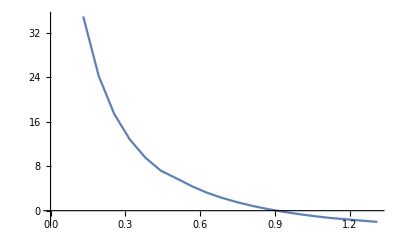

```mathematica
ListLinePlot[Thread[{Rb,A18Beta}]]
```

#### Plotting the chord length

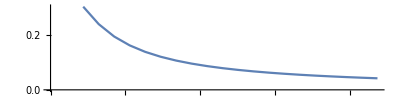

```mathematica
ListLinePlot[Thread[{Rb,A18lengthList}], AspectRatio->.25]
```

### Airfoil BW3

#### “Tangential Force Coefficient” (CFT) and “Normal Force Coefficient “(CFN) in function of attack angle “α” and the speed ratio “λ”

```mathematica
BW3CFT[α_, λ_]:= BW3FCL[α] Sin[theta[λ]Degree]-BW3FCD[α] Cos[theta[λ] Degree];
BW3CFN[α_, λ_]:= BW3FCL[α] Cos[theta[λ] Degree]+BW3FCD[α] Sin[theta[λ] Degree];
```

```mathematica
Plot3D[{BW3CFT[α,λ], BW3CFN[α,λ]},{α,-8,12},{λ,0,λd}]
```

-Graphics3D-

#### Max attact angle

```mathematica
αlim1 = 18;
αlim2 = -8;
```

```mathematica
BW3MaxAngle=α/. FindMaximum[{BW3FCL[α], α ≥αlim2 && α ≤αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]]
```

14.1699

#### Calculating the chord length

```mathematica
BW3Length= AverageChordLength[R1, .3,BW3FCL[BW3MaxAngle], Z1]
```

0.0774053

#### Calculating the solidity

```mathematica
BW3Solidity = Solidity[R1,BW3Length,Z1]
```

0.0564249

#### Calculating the maximum CL for speed ratio

```mathematica
BW3MaxCFT = Map[getMaxValue1,BW3CFT[α,λr1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{1.14409,0.891745,0.713655,0.58786,0.495843,0.42637,0.372748,0.330008,0.295221,0.266416,0.24222,0.221629,0.204624,0.189392,0.176012,0.164169,0.153614,0.14415,0.135615,0.127881}

#### Calculating the angle for the maximum CL for speed ratio

```mathematica
BW3MaxAlpha = Map[getMaxValue2,BW3CFT[α,λr1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{13.7579,13.4924,13.2939,13.0015,12.9998,12.3832,12.2582,12.2188,12.1229,12.0111,11.8565,11.742,10.8805,10.8508,10.8229,10.7963,10.771,10.75,10.7342,10.711}

#### Calculating the pitch angle

```mathematica
BW3Beta =(θs1 -BW3MaxAlpha)
```

{30.4268,19.9136,13.23,8.87163,5.56025,3.71198,1.93814,0.472779,-0.651521,-1.54829,-2.24072,-2.84746,-2.60721,-3.11819,-3.56489,-3.95838,-4.30735,-4.62192,-4.90863,-5.15962}

#### Calculating the chords

```mathematica
BW3lengthList = ChordLength[Rb,Vw, Z1, BW3FCL[BW3MaxAngle], λr1, Vrs1]
```

{0.219642,0.173504,0.140731,0.117405,0.100307,0.0873665,0.0772855,0.0692363,0.0626738,0.057228,0.0526404,0.0487253,0.0453465,0.0424018,0.0398134,0.0375206,0.0354759,0.0336413,0.0319863,0.0304856}

#### Showing the results in table form

```mathematica
Thread[{Rb,BW3lengthList,BW3Beta }] //TableForm
```

0.131 | 0.219642 | 30.4268
0.193053 | 0.173504 | 19.9136
0.255105 | 0.140731 | 13.23
0.317158 | 0.117405 | 8.87163
0.379211 | 0.100307 | 5.56025
0.441263 | 0.0873665 | 3.71198
0.503316 | 0.0772855 | 1.93814
0.565368 | 0.0692363 | 0.472779
0.627421 | 0.0626738 | -0.651521
0.689474 | 0.057228 | -1.54829
0.751526 | 0.0526404 | -2.24072
0.813579 | 0.0487253 | -2.84746
0.875632 | 0.0453465 | -2.60721
0.937684 | 0.0424018 | -3.11819
0.999737 | 0.0398134 | -3.56489
1.06179 | 0.0375206 | -3.95838
1.12384 | 0.0354759 | -4.30735
1.18589 | 0.0336413 | -4.62192
1.24795 | 0.0319863 | -4.90863
1.31 | 0.0304856 | -5.15962

```mathematica
Export[".\\WTBDesign\\BW3\\design_data.xls",Thread[{Rb,BW3lengthList,BW3Beta }],"XLS"]
```

Export::nodir: Directory C:\Users\Jesus Rocha\Documents\WTBDesign\BW3\ does not exist.

Export::noopen: Cannot open .\WTBDesign\BW3\design_data.xls.

$Failed

#### Plotting the twist

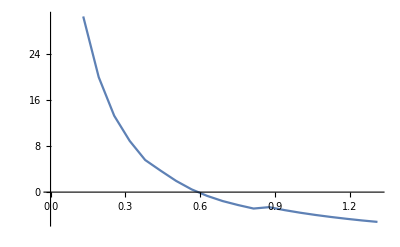

```mathematica
ListLinePlot[Thread[{Rb,BW3Beta}]]
```

#### Plotting the chord length

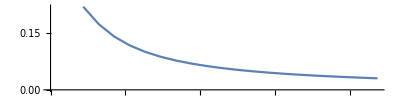

```mathematica
ListLinePlot[Thread[{Rb,BW3lengthList}], AspectRatio->.25]
```

### Airfoil NACA63A210

#### “Tangential Force Coefficient” (CFT) and “Normal Force Coefficient “(CFN) in function of attack angle “α” and the speed ratio “λ”

```mathematica
NACA63A210CFT[α_, λ_]:= NACA63A210FCL[α] Sin[theta[λ]Degree]-NACA63A210FCD[α] Cos[theta[λ] Degree];
NACA63A210CFN[α_, λ_]:= NACA63A210FCL[α] Cos[theta[λ] Degree]+NACA63A210FCD[α] Sin[theta[λ] Degree];
```

```mathematica
Plot3D[{NACA63A210CFT[α,λ], NACA63A210CFN[α,λ]},{α,-8,12},{λ,0,λd}]
```

-Graphics3D-

#### Max attact angle

```mathematica
αlim1 = 14;
αlim2 = -11;
```

```mathematica
NACA63A210MaxAngle=α/. FindMaximum[{NACA63A210FCL[α], α ≥αlim2 && α ≤αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]]
```

12.0875

#### Calculating the chord length

```mathematica
NACA63A210Length= AverageChordLength[R1, .3,NACA63A210FCL[NACA63A210MaxAngle], Z1]
```

0.110617

#### Calculating the solidity

```mathematica
NACA63A210Solidity = Solidity[R1,NACA63A210Length,Z1]
```

0.0806347

#### Calculating the maximum CL for speed ratio

```mathematica
NACA63A210MaxCFT = Map[getMaxValue1,NACA63A210CFT[α,λr1]]
```

{0.797644,0.620402,0.495547,0.407115,0.34252,0.293743,0.255832,0.225636,0.201081,0.180759,0.163687,0.149156,0.13665,0.125781,0.116254,0.107838,0.100352,0.0936531,0.0876235,0.0811329}

#### Calculating the angle for the maximum CL for speed ratio

```mathematica
NACA63A210MaxAlpha = Map[getMaxValue2,NACA63A210CFT[α,λr1]]
```

{11.6187,11.4665,11.3804,11.3119,11.253,11.2294,11.1705,11.1085,11.0438,10.9718,10.9069,10.8434,10.7813,10.7179,10.6596,10.6039,10.5508,10.5002,10.4571,9.39145}

#### Calculating the pitch angle

```mathematica
NACA63A210Beta =(θs1 -NACA63A210MaxAlpha)
```

{32.566,21.9396,15.1435,10.5613,7.30705,4.86579,3.02581,1.58309,0.427541,-0.508975,-1.29117,-1.94884,-2.50798,-2.9853,-3.40167,-3.76596,-4.08709,-4.37206,-4.63156,-3.84008}

#### Calculating the chords

```mathematica
NACA63A210lengthList = ChordLength[Rb,Vw, Z1, NACA63A210FCL[NACA63A210MaxAngle], λr1, Vrs1]
```

{0.313881,0.247948,0.201113,0.167779,0.143345,0.124852,0.110446,0.0989429,0.0895647,0.0817824,0.0752264,0.0696314,0.0648029,0.0605948,0.0568957,0.0536192,0.0506973,0.0480756,0.0457103,0.0435659}

#### Showing the results in table form

```mathematica
Thread[{Rb,NACA63A210lengthList,NACA63A210Beta }] //TableForm
```

0.131 | 0.313881 | 32.566
0.193053 | 0.247948 | 21.9396
0.255105 | 0.201113 | 15.1435
0.317158 | 0.167779 | 10.5613
0.379211 | 0.143345 | 7.30705
0.441263 | 0.124852 | 4.86579
0.503316 | 0.110446 | 3.02581
0.565368 | 0.0989429 | 1.58309
0.627421 | 0.0895647 | 0.427541
0.689474 | 0.0817824 | -0.508975
0.751526 | 0.0752264 | -1.29117
0.813579 | 0.0696314 | -1.94884
0.875632 | 0.0648029 | -2.50798
0.937684 | 0.0605948 | -2.9853
0.999737 | 0.0568957 | -3.40167
1.06179 | 0.0536192 | -3.76596
1.12384 | 0.0506973 | -4.08709
1.18589 | 0.0480756 | -4.37206
1.24795 | 0.0457103 | -4.63156
1.31 | 0.0435659 | -3.84008

```mathematica
Export[".\\WTBDesign\\NACA63A210\\design_data.xls",Thread[{Rb,NACA63A210lengthList,NACA63A210Beta }],"XLS"]
```

Export::nodir: Directory C:\Users\Jesus Rocha\Documents\WTBDesign\NACA63A210\ does not exist.

Export::noopen: Cannot open .\WTBDesign\NACA63A210\design_data.xls.

$Failed

#### Plotting the twist

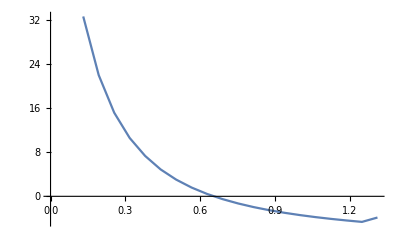

```mathematica
ListLinePlot[Thread[{Rb,NACA63A210Beta}]]
```

#### Plotting the chord length

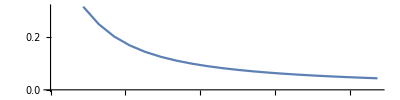

```mathematica
ListLinePlot[Thread[{Rb,NACA63A210lengthList}], AspectRatio->.25]
```

### Airfoil NACA4415

#### “Tangential Force Coefficient” (CFT) and “Normal Force Coefficient “(CFN) in function of attack angle “α” and the speed ratio “λ”

```mathematica
NACA4415CFT[α_, λ_]:= NACA4415FCL[α] Sin[theta[λ]Degree]-NACA4415FCD[α] Cos[theta[λ] Degree];
NACA4415CFN[α_, λ_]:= NACA4415FCL[α] Cos[theta[λ] Degree]+NACA4415FCD[α] Sin[theta[λ] Degree];
```

```mathematica
Plot3D[{NACA4415CFT[α,λ], NACA4415CFN[α,λ]},{α,-8,12},{λ,0,λd}]
```

-Graphics3D-

#### Max attact angle

```mathematica
αlim1 = 19;
αlim2 = -15;
```

```mathematica
NACA4415MaxAngle=α/. FindMaximum[{NACA4415FCL[α], α ≥αlim2 && α ≤αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

15.751

#### Calculating the chord length

```mathematica
NACA4415Length= AverageChordLength[R1, .3,NACA4415FCL[NACA4415MaxAngle], Z1]
```

0.0908083

#### Calculating the solidity

```mathematica
NACA4415Solidity = Solidity[R1,NACA4415Length,Z1]
```

0.0661951

#### Calculating the maximum CL for speed ratio

```mathematica
NACA4415MaxCFT = Map[getMaxValue1,NACA4415CFT[α,λr1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

{0.971821,0.756375,0.605142,0.497942,0.419994,0.361156,0.31539,0.279014,0.249499,0.225044,0.204453,0.186887,0.172002,0.158953,0.147484,0.137333,0.128338,0.120359,0.113175,0.106673}

#### Calculating the angle for the maximum CL for speed ratio

```mathematica
NACA4415MaxAlpha = Map[getMaxValue2,NACA4415CFT[α,λr1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

{14.75,14.7476,14.25,13.9151,13.7775,13.7491,13.6816,13.3415,13.2756,13.25,13.25,13.2379,12.75,12.75,12.746,12.712,12.1632,12.0818,12.0176,12.}

#### Calculating the pitch angle

```mathematica
NACA4415Beta =(θs1 -NACA4415MaxAlpha)
```

{29.4347,18.6584,12.2739,7.95802,4.78256,2.34605,0.514743,-0.64993,-1.80423,-2.78718,-3.6342,-4.34329,-4.47671,-5.01735,-5.48801,-5.87409,-5.69956,-5.95373,-6.19203,-6.44864}

#### Calculating the chords

```mathematica
NACA4415lengthList = ChordLength[Rb,Vw, Z1, NACA4415FCL[NACA4415MaxAngle], λr1, Vrs1]
```

{0.257673,0.203547,0.165099,0.137734,0.117676,0.102494,0.0906678,0.0812248,0.073526,0.0671373,0.0617553,0.0571622,0.0531984,0.0497438,0.0467072,0.0440174,0.0416187,0.0394665,0.0375248,0.0357643}

#### Showing the results in table form

```mathematica
Thread[{Rb,NACA4415lengthList,NACA4415Beta }] //TableForm
```

0.131 | 0.257673 | 29.4347
0.193053 | 0.203547 | 18.6584
0.255105 | 0.165099 | 12.2739
0.317158 | 0.137734 | 7.95802
0.379211 | 0.117676 | 4.78256
0.441263 | 0.102494 | 2.34605
0.503316 | 0.0906678 | 0.514743
0.565368 | 0.0812248 | -0.64993
0.627421 | 0.073526 | -1.80423
0.689474 | 0.0671373 | -2.78718
0.751526 | 0.0617553 | -3.6342
0.813579 | 0.0571622 | -4.34329
0.875632 | 0.0531984 | -4.47671
0.937684 | 0.0497438 | -5.01735
0.999737 | 0.0467072 | -5.48801
1.06179 | 0.0440174 | -5.87409
1.12384 | 0.0416187 | -5.69956
1.18589 | 0.0394665 | -5.95373
1.24795 | 0.0375248 | -6.19203
1.31 | 0.0357643 | -6.44864

```mathematica
Export[".\\WTBDesign\\NACA4415\\design_data.xls",Thread[{Rb,NACA4415lengthList,NACA4415Beta }],"XLS"]
```

Export::nodir: Directory C:\Users\Jesus Rocha\Documents\WTBDesign\NACA4415\ does not exist.

Export::noopen: Cannot open .\WTBDesign\NACA4415\design_data.xls.

$Failed

#### Plotting the twist

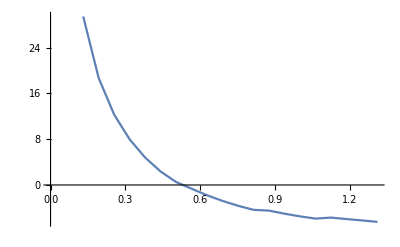

```mathematica
ListLinePlot[Thread[{Rb,NACA4415Beta}]]
```

#### Plotting the chord length

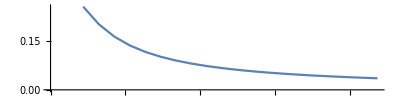

```mathematica
ListLinePlot[Thread[{Rb,NACA4415lengthList}], AspectRatio->.25]
```

## Power Generation

### Common Calculations

#### Averaged Sections

```mathematica
For[i = 1; Rb2 = {}, i < Length[Rb], i++, AppendTo[Rb2, (Rb[[i]] + Rb[[i + 1]]) /2]]
Rb2
```

{0.162026,0.224079,0.286132,0.348184,0.410237,0.472289,0.534342,0.596395,0.658447,0.7205,0.782553,0.844605,0.906658,0.968711,1.03076,1.09282,1.15487,1.21692,1.27897}

#### Speed Ratio for Averaged Sections

```mathematica
λr2 =λd Rb2 / R1
```

{0.848368,1.17327,1.49818,1.82309,2.148,2.4729,2.79781,3.12272,3.44762,3.77253,4.09744,4.42234,4.74725,5.07216,5.39706,5.72197,6.04688,6.37178,6.69669}

### Airfoil A18

#### Average Length Sections

```mathematica
For[i = 1; A18lengthList2 = {}, i < Length[A18lengthList], i++, AppendTo[A18lengthList2, (A18lengthList[[i]] + A18lengthList[[i + 1]]) /2]]
A18lengthList2
```

{0.273427,0.218545,0.179529,0.151415,0.130524,0.114513,0.101904,0.0917413,0.0833898,0.0764117,0.0704982,0.0654254,0.0610275,0.0571793,0.0537845,0.0507679,0.0480699,0.0456429,0.0434482}

#### Average Pitch Angles

```mathematica
For[i = 1; A18Beta2  = {}, i < Length[A18Beta], i++, AppendTo[A18Beta2 , (A18Beta[[i]] + A18Beta[[i + 1]]) /2]]
A18Beta2
```

{29.6025,20.8321,15.1311,11.2111,8.39967,6.5308,5.13716,3.82682,2.74812,1.87636,1.14664,0.529232,0.00646681,-0.441669,-0.831725,-1.16903,-1.44006,-1.6764,-1.90874}

#### Forces along the blade

```mathematica
A18TFList = Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
A18NFList = Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
Export["D:\\Shared\\Chuy\\WTBDesign\\A18\\force_data.xls",Thread[{Rb2,Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr],Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr] }],"XLS"]
```

D:\Shared\Chuy\WTBDesign\A18\force_data.xls

```mathematica
A18TF[V_]:=Piecewise[{
{ Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18NF[V_]:=Piecewise[{
{ Total[Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFN[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18CT[V_]:= (2 A18TF[V])/(δa π V^2 R1^2)
```

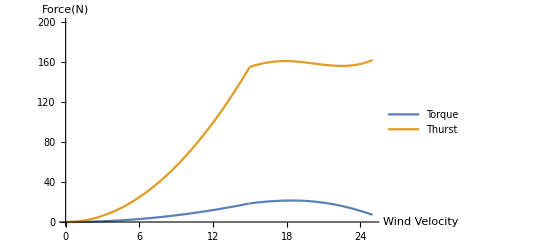

```mathematica
Plot[{A18TF[v], A18NF[v]} ,{v,0,Vw +10}, PlotRange->{0,200},AxesLabel->{"Wind Velocity", "Force(N)"} ,PlotLegends->{"Torque","Thurst"}]
```

```mathematica
A18TF[Vw]
A18NF[Vw]
```

18.6661

155.505

#### Out Power

```mathematica
A18Po[V_]:=Piecewise[{
{ (Z1 π)/30 RPM[V, λd, R1] Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] ≤ rpm1 },

{ (Z1 π)/30 rpm1 Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] > rpm1 }
}]
```

```mathematica
A18Po[Vw]
```

5761.5

```mathematica
Pw[Vw, R1, 1]
```

11144.8

```mathematica
A18Po[Vw]/Pw[Vw, R1, 1]
```

0.516967

```mathematica
A18Po[15]/Pw[15, R1, 1]
```

0.516967

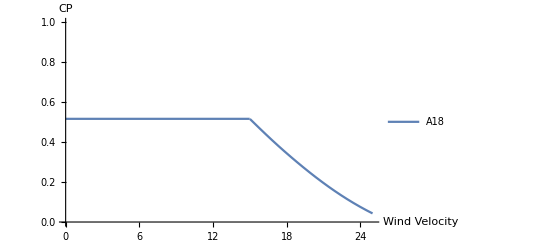

```mathematica
Plot[{A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +10}, PlotRange->{0,1},AxesLabel->{"Wind Velocity", "CP"} ,PlotLegends->{"A18"}]
```

### Airfoil BW3

#### Average Length Sections

```mathematica
For[i = 1; BW3lengthList2 = {}, i < Length[BW3lengthList], i++, AppendTo[BW3lengthList2, (BW3lengthList[[i]] + BW3lengthList[[i + 1]]) /2]]
BW3lengthList2
```

{0.196573,0.157118,0.129068,0.108856,0.0938368,0.082326,0.0732609,0.065955,0.0599509,0.0549342,0.0506828,0.0470359,0.0438741,0.0411076,0.038667,0.0364983,0.0345586,0.0328138,0.0312359}

#### Average Pitch Angles

```mathematica
For[i = 1; BW3Beta2  = {}, i < Length[BW3Beta], i++, AppendTo[BW3Beta2 , (BW3Beta[[i]] + BW3Beta[[i + 1]]) /2]]
BW3Beta2
```

{25.1702,16.5718,11.0508,7.21594,4.63611,2.82506,1.20546,-0.0893709,-1.0999,-1.8945,-2.54409,-2.72733,-2.8627,-3.34154,-3.76163,-4.13286,-4.46463,-4.76528,-5.03413}

#### Forces along the blade

```mathematica
BW3TF[V_]:=Piecewise[{
{ Total[Fblade[BW3CFT[theta[λr2]-BW3Beta2, λr2], Vr[V, V λr2], BW3lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[BW3CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-BW3Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], BW3lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
BW3NF[V_]:=Piecewise[{
{ Total[Fblade[BW3CFN[theta[λr2]-BW3Beta2, λr2], Vr[V, V λr2], BW3lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[BW3CFN[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-BW3Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], BW3lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
BW3CT[V_]:= (2 BW3TF[V])/(δa π V^2 R1^2);
```

```mathematica
BW3TFList = Fblade[BW3CFT[theta[λr2]-BW3Beta2, λr2], Vr[Vw, Vw λr2], BW3lengthList2, Δr];
```

```mathematica
BW3NFList = Fblade[BW3CFN[theta[λr2]-BW3Beta2, λr2], Vr[Vw, Vw λr2], BW3lengthList2, Δr];
```

```mathematica
Export[".\\WTBDesign\\BW3\\force_data.xls",Thread[{Rb2,Fblade[BW3CFT[theta[λr2]-BW3Beta2, λr2], Vr[Vw, Vw λr2], BW3lengthList2, Δr],Fblade[BW3CFN[theta[λr2]-BW3Beta2, λr2], Vr[Vw, Vw λr2], BW3lengthList2, Δr] }],"XLS"]
```

Export::nodir: Directory C:\Users\Jesus Rocha\Documents\WTBDesign\BW3\ does not exist.

Export::noopen: Cannot open .\WTBDesign\BW3\force_data.xls.

$Failed

#### Out Power

```mathematica
BW3Po[V_]:=Piecewise[{
{ (Z1 π)/30 RPM[V, λd, R1] Total[Fblade[BW3CFT[theta[λr2]-BW3Beta2, λr2], Vr[V, V λr2], BW3lengthList2, Δr] Rb2],  RPM[V,λd, R1] ≤ rpm1 },

{ (Z1 π)/30 rpm1 Total[Fblade[BW3CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-BW3Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], BW3lengthList2, Δr] Rb2],  RPM[V,λd, R1] > rpm1 }
}]
```

```mathematica
BW3Po[Vw]
```

5514.4

```mathematica
Pw[Vw, R1, 1]
```

11144.8

```mathematica
BW3Po[Vw]/Pw[Vw, R1, 1]
```

0.494796

### Airfoil NACA63A210

#### Average Length Sections

```mathematica
For[i = 1; NACA63A210lengthList2 = {}, i < Length[NACA63A210lengthList], i++, AppendTo[NACA63A210lengthList2, (NACA63A210lengthList[[i]] + NACA63A210lengthList[[i + 1]]) /2]]
NACA63A210lengthList2
```

{0.280915,0.224531,0.184446,0.155562,0.134099,0.117649,0.104694,0.0942538,0.0856736,0.0785044,0.0724289,0.0672172,0.0626989,0.0587453,0.0552575,0.0521583,0.0493864,0.0468929,0.0446381}

#### Average Pitch Angles

```mathematica
For[i = 1; NACA63A210Beta2  = {}, i < Length[NACA63A210Beta], i++, AppendTo[NACA63A210Beta2 , (NACA63A210Beta[[i]] + NACA63A210Beta[[i + 1]]) /2]]
NACA63A210Beta2
```

{27.2528,18.5415,12.8524,8.93416,6.08642,3.9458,2.30445,1.00532,-0.0407172,-0.900072,-1.62,-2.22841,-2.74664,-3.19349,-3.58382,-3.92653,-4.22958,-4.50181,-4.23582}

#### Forces along the blade

```mathematica
NACA63A210TF[V_]:=Piecewise[{
{ Total[Fblade[NACA63A210CFT[theta[λr2]-NACA63A210Beta2, λr2], Vr[V, V λr2], NACA63A210lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[NACA63A210CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-NACA63A210Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], NACA63A210lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
NACA63A210NF[V_]:=Piecewise[{
{ Total[Fblade[NACA63A210CFN[theta[λr2]-NACA63A210Beta2, λr2], Vr[V, V λr2], NACA63A210lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[NACA63A210CFN[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-NACA63A210Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], NACA63A210lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
NACA63A210CT[V_]:= (2 NACA63A210TF[V])/(δa π V^2 R1^2);
```

```mathematica
NACA63A210TFList = Fblade[NACA63A210CFT[theta[λr2]-NACA63A210Beta2, λr2], Vr[Vw, Vw λr2], NACA63A210lengthList2, Δr];
```

```mathematica
NACA63A210NFList = Fblade[NACA63A210CFN[theta[λr2]-NACA63A210Beta2, λr2], Vr[Vw, Vw λr2], NACA63A210lengthList2, Δr];
```

```mathematica
Export[".\\WTBDesign\\NACA63A210\\force_data.xls",Thread[{Rb2,Fblade[NACA63A210CFT[theta[λr2]-NACA63A210Beta2, λr2], Vr[Vw, Vw λr2], NACA63A210lengthList2, Δr],Fblade[NACA63A210CFN[theta[λr2]-NACA63A210Beta2, λr2], Vr[Vw, Vw λr2], NACA63A210lengthList2, Δr] }],"XLS"]
```

Export::nodir: Directory C:\Users\Jesus Rocha\Documents\WTBDesign\NACA63A210\ does not exist.

Export::noopen: Cannot open .\WTBDesign\NACA63A210\force_data.xls.

$Failed

#### Out Power

```mathematica
NACA63A210Po[V_]:=Piecewise[{
{ (Z1 π)/30 RPM[V, λd, R1] Total[Fblade[NACA63A210CFT[theta[λr2]-NACA63A210Beta2, λr2], Vr[V, V λr2], NACA63A210lengthList2, Δr] Rb2],  RPM[V,λd, R1] ≤ rpm1 },

{ (Z1 π)/30 rpm1 Total[Fblade[NACA63A210CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-NACA63A210Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], NACA63A210lengthList2, Δr] Rb2],  RPM[V,λd, R1] > rpm1 }
}]
```

```mathematica
NACA63A210Po[Vw]
```

5254.

```mathematica
Pw[Vw, R1, 1]
```

11144.8

```mathematica
NACA63A210Po[Vw]/Pw[Vw, R1, 1]
```

0.47143

### Airfoil NACA4415

#### Average Length Sections

```mathematica
For[i = 1; NACA4415lengthList2 = {}, i < Length[NACA4415lengthList], i++, AppendTo[NACA4415lengthList2, (NACA4415lengthList[[i]] + NACA4415lengthList[[i + 1]]) /2]]
NACA4415lengthList2
```

{0.23061,0.184323,0.151416,0.127705,0.110085,0.096581,0.0859463,0.0773754,0.0703316,0.0644463,0.0594587,0.0551803,0.0514711,0.0482255,0.0453623,0.0428181,0.0405426,0.0384956,0.0366446}

#### Average Pitch Angles

```mathematica
For[i = 1; NACA4415Beta2  = {}, i < Length[NACA4415Beta], i++, AppendTo[NACA4415Beta2 , (NACA4415Beta[[i]] + NACA4415Beta[[i + 1]]) /2]]
NACA4415Beta2
```

{24.0466,15.4662,10.116,6.37029,3.5643,1.4304,-0.0675933,-1.22708,-2.29571,-3.21069,-3.98875,-4.41,-4.74703,-5.25268,-5.68105,-5.78682,-5.82664,-6.07288,-6.32034}

#### Forces along the blade

```mathematica
NACA4415TF[V_]:=Piecewise[{
{ Total[Fblade[NACA4415CFT[theta[λr2]-NACA4415Beta2, λr2], Vr[V, V λr2], NACA4415lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[NACA4415CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-NACA4415Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], NACA4415lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
NACA4415NF[V_]:=Piecewise[{
{ Total[Fblade[NACA4415CFN[theta[λr2]-NACA4415Beta2, λr2], Vr[V, V λr2], NACA4415lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[NACA4415CFN[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-NACA4415Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], NACA4415lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
NACA4415CT[V_]:= (2 NACA4415TF[V])/(δa π V^2 R1^2);
```

```mathematica
NACA4415TFList = Fblade[NACA4415CFT[theta[λr2]-NACA4415Beta2, λr2], Vr[Vw, Vw λr2], NACA4415lengthList2, Δr];
```

```mathematica
NACA4415NFList = Fblade[NACA4415CFN[theta[λr2]-NACA4415Beta2, λr2], Vr[Vw, Vw λr2], NACA4415lengthList2, Δr];
```

```mathematica
Export[".\\WTBDesign\\NACA4415\\force_data.xls",Thread[{Rb2,Fblade[NACA4415CFT[theta[λr2]-NACA4415Beta2, λr2], Vr[Vw, Vw λr2], NACA4415lengthList2, Δr],Fblade[NACA4415CFN[theta[λr2]-NACA4415Beta2, λr2], Vr[Vw, Vw λr2], NACA4415lengthList2, Δr] }],"XLS"]
```

Export::nodir: Directory C:\Users\Jesus Rocha\Documents\WTBDesign\NACA4415\ does not exist.

Export::noopen: Cannot open .\WTBDesign\NACA4415\force_data.xls.

$Failed

```mathematica
".\\WTBDesign\\NACA4415\\force_data.xls"
```

.\WTBDesign\NACA4415\force_data.xls

#### Out Power

```mathematica
NACA4415Po[V_]:=Piecewise[{
{ (Z1 π)/30 RPM[V, λd, R1] Total[Fblade[NACA4415CFT[theta[λr2]-NACA4415Beta2, λr2], Vr[V, V λr2], NACA4415lengthList2, Δr] Rb2],  RPM[V,λd, R1] ≤ rpm1 },

{ (Z1 π)/30 rpm1 Total[Fblade[NACA4415CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-NACA4415Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], NACA4415lengthList2, Δr] Rb2],  RPM[V,λd, R1] > rpm1 }
}]
```

```mathematica
NACA4415Po[Vw]
```

5437.22

```mathematica
Pw[Vw, R1, 1]
```

11144.8

```mathematica
NACA4415Po[Vw]/Pw[Vw, R1, 1]
```

0.48787

### Comparison

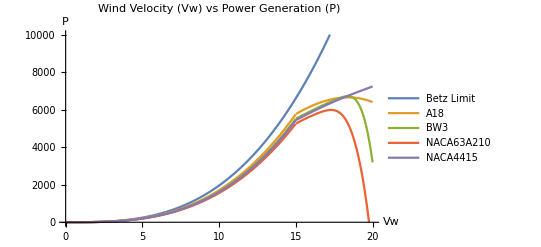

```mathematica
Plot[{Pw[v, R1, CPmax], A18Po[v], BW3Po[v], NACA63A210Po[v],NACA4415Po[v]} ,{v,0,Vw +5}, PlotRange->{0,10000},PlotLabel->Style["Wind Velocity (Vw) vs Power Generation (P)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["P", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18","BW3", "NACA63A210", "NACA4415"}]
```

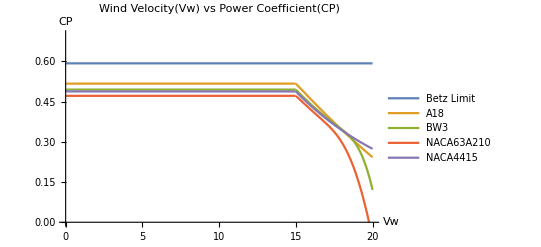

```mathematica
Plot[{Pw[v, R1, CPmax]/Pw[v, R1, 1],A18Po[v]/Pw[v, R1, 1], BW3Po[v]/Pw[v, R1, 1], NACA63A210Po[v]/Pw[v, R1, 1],NACA4415Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +5}, PlotRange->{0,.7},PlotLabel->Style["Wind Velocity(Vw) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18","BW3", "NACA63A210", "NACA4415"}]
```

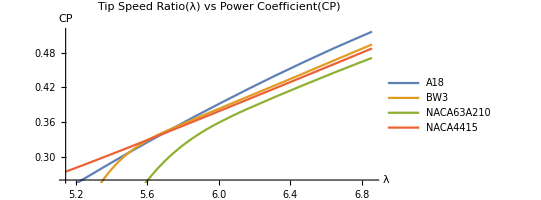

```mathematica
ParametricPlot[{{TSRD[v],A18Po[v]/Pw[v, R1, 1]}, {TSRD[v],BW3Po[v]/Pw[v, R1, 1]}, {TSRD[v],NACA63A210Po[v]/Pw[v, R1, 1]},{TSRD[v],NACA4415Po[v]/Pw[v, R1, 1]}} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18","BW3", "NACA63A210", "NACA4415"}, AspectRatio->1/2]
```

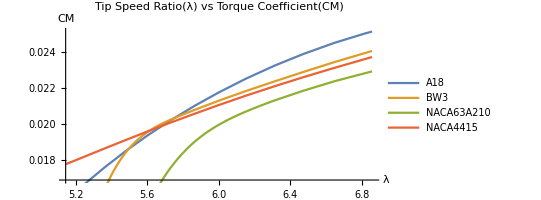

```mathematica
ParametricPlot[{{TSRD[v],A18CT[v]}, {TSRD[v],BW3CT[v]}, {TSRD[v],NACA63A210CT[v]},{TSRD[v],NACA4415CT[v]}} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Torque Coefficient(CM)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CM", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18","BW3", "NACA63A210", "NACA4415"}, AspectRatio->1/2]
```